# Singular Spectrum Analysis

## make test data

```mathematica
len=200
```

200

## line

```mathematica
a1=Table[N[2*i/len],{i,len}];
```

```mathematica
Export["~/ssa_20211008/graph1.csv",a1,"CSV"]
```

~/ssa_20211008/graph1.csv

## line

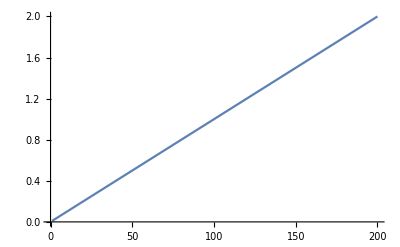

```mathematica
ListPlot[a1,Joined->True]
```

## sine wave

```mathematica
a2=Table[0.5*Sin[2Pi(20*i/len)],{i,len}];
```

```mathematica
Export["~/ssa_20211008/graph2.csv",a2,"CSV"]
```

~/ssa_20211008/graph2.csv

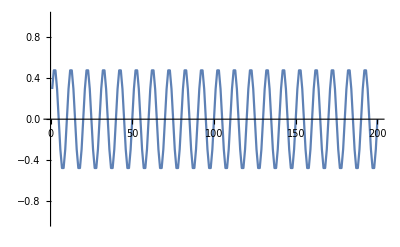

```mathematica
ListPlot[a2,Joined->True,PlotRange->{-1,1}]
```

## superposition of curves

```mathematica
c=a1+a2;
```

```mathematica
Export["~/ssa_20211008/graph3.csv",c,"CSV"]
```

~/ssa_20211008/graph3.csv

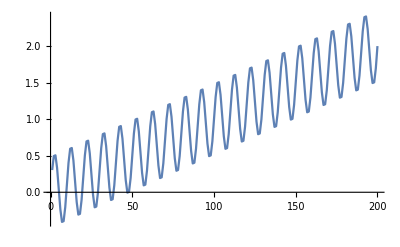

```mathematica
ListPlot[c,Joined->True]
```

## decomposition of curve by singular spectral analysis

```mathematica
c[[1]]
```

0.303893

```mathematica
Length[c]
```

200

200

200

0

```mathematica
Dimensions[c]
```

{200}

{200}

{200}

```mathematica
m=Length[c]
```

200

```mathematica
n=Floor[m/2]
```

100

```mathematica
m-n+1
```

101

```mathematica
%+n
```

201

```mathematica
x=N[Table[c[[i+j-1]],{i,m-n+1},{j,n}]];
```

```mathematica
Dimensions[x]
```

{101,100}

```mathematica
?SingularValueDecomposition
```

```mathematica
uu=SingularValueDecomposition[x];
```

```mathematica
Dimensions[uu]
```

{3}

```mathematica
u=uu[[1]];
```

```mathematica
w=uu[[2]];
```

```mathematica
v=uu[[3]];
```

```mathematica
Dimensions[u]
```

{101,101}

```mathematica
Dimensions[w]
```

{101,100}

```mathematica
Dimensions[v]
```

{100,100}

```mathematica
Print[n]
```

100

## distribution of singular values

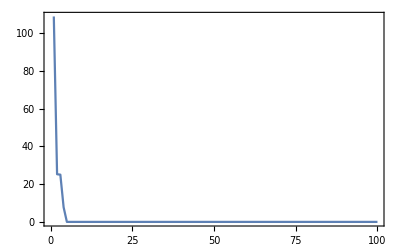

```mathematica
ListPlot[Table[{i,w[[i,i]]},{i,n}],Joined->True,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
sn[xx_]:=Module[{i,j,k,n,n1,x,sum},x={};
{n1,n}=Dimensions[xx];
j=0;sum=0;
Do[Do[If[k≤n,sum=sum+xx[[i-k+1,k]];j=j+1],{k,i}];
x=Append[x,sum/j];sum=0;j=0,{i,n1}];
j=0;sum=0;
     Do[Do[If[k≤n1,sum=sum+xx[[n1-k+1,k+i-1]];j=j+1],{k,n-i+1}];
x=Append[x,sum/j];sum=0;j=0,{i,2,n}];
Return[x]]
```

## 0

## trend

```mathematica
xx=Sum[w[[i,i]]Outer[Times,Transpose[u][[i]],Transpose[v][[i]]],{i,1}];
```

```mathematica
y1=sn[xx];
```

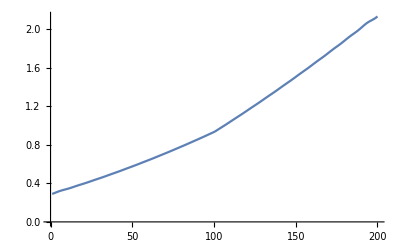

```mathematica
ListPlot[y1,Joined->True,PlotRange->All]
```

## elements except trend

```mathematica
xx=Sum[w[[i,i]]Outer[Times,Transpose[u][[i]],Transpose[v][[i]]],{i,2,3}];
```

```mathematica
y1=sn[xx];
```

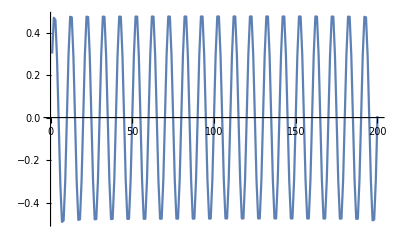

```mathematica
ListPlot[y1,Joined->True]
```